# Final Exam

Note: If you get to a part where you know exactly what you need to do but don’t know how to make Mathematica do it, please write clearly and explicitly what you would do. We will give you at least partial credit for correct reasoning even if the code doesn’t quite work. (But do your best to get the code to work! All Mathematica techniques you will need for this exam you have already seen in some form in the homework.)

## Problem 12

A charged particle of mass m = 0.03 kg and charge q = 0.2×10^-6C is constrained to move along the x axis. A second charged particle with Q = -1×10^-6 C is fixed in place at a position (x, y) = (0, 0.05 m). Calculate the period of oscillation if the charge q is released from rest at a position x = – 0.1255 m. The nearest tenth of a second is sufficient. Note that the potential energy between two charges is U = k q_1 q_2  / r, where k = 8.99 ×10^9 N m^2/C^2. 
-Graphics-

```mathematica
Quit[]
Clear["`*"]
```

```mathematica
k =8.99*10^9;
q = 0.2*10^-6;
Q = -1*10^-6;
m = 0.03;
x0=-0.1255;
v0 = 0;
```

```mathematica
U = (k*q*Q)/(Sqrt[x^2+0.05^2]);
T = (1/2)*m*xdot^2;
L = T-U
```

0.001798/(√(0.0025+x^2))+0.015 xdot^2

```mathematica
dLdx = D[L,x]/.{x->x[t],xdot->x'[t]};
dLdxdot = D[L,xdot]/.{x->x[t],xdot->x'[t]};
eq1 = dLdx == D[dLdxdot,t]
```

-(0.001798 x[t])/((0.0025+x[t]^2)^(3/2))==0.03 x''[t]

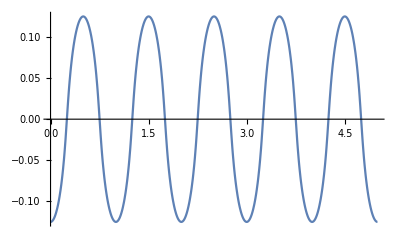

```mathematica
bc = {x[0]==x0,x'[0]==v0};
sol = NDSolve[{eq1,bc},x[t],{t,0,5}];
Plot[x[t]/.sol,{t,0,5}]
```

The period of oscillation is: 1 sec

## Additional work for any of the written problems (label each one clearly)

```mathematica
Quit[]
```

{{x→0},{x→-(√2 √(-b+r))/(√r)},{x→(√2 √(-b+r))/(√r)}}

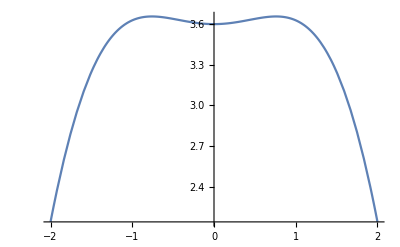

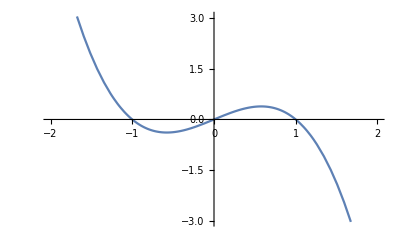

```mathematica
(*problem 3*)
Solve[-b*x+r*x-(r*x^3)/2==0,x]
Plot[((1.6+2)*Cos[x]+2*x*Sin[x]),{x,-2,2}]
Plot[-1*x+2*x-(2*x^3)/2,{x,-2,2}]
```

```mathematica
(*problem 8*)
Integrate[x^2*(((3*m)/(2*L))*(1-(x/L)^2)),{x,0,L}];
Integrate[(1/(2*m))*x*(((3*m)/(2*L))*(1-(x/L)^2)),{x,0,L}]+(L/2);
```

```mathematica
Quit[]
```

```mathematica
(*problem 10*)
DSolve[x''[t]*(1-(1/(1+2)))==(-1/1)*x[t],x[t],t]
DSolve[x''[t]==(-1/2)*x[t],x[t],t]
```

{{x[t]→C[1] Cos[√(3/2) t]+C[2] Sin[√(3/2) t]}}

{{x[t]→C[1] Cos[t/(√2)]+C[2] Sin[t/(√2)]}}